```mathematica
Quit[]
```

## Import astro

InterpolatingFunction[…]

1.79423×10^-9

0.

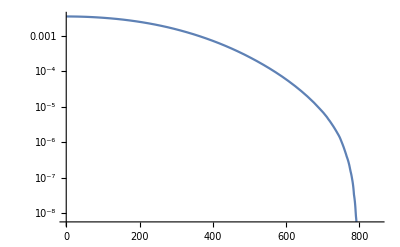

```mathematica
SetDirectory[NotebookDirectory[]];
Lgvmin=Import["../gvmin_round.dat"];
ResetDirectory[];
fgvmin=Interpolation[Lgvmin,InterpolationOrder->1]
fgvmin[794]
fgvmin[795]

LogPlot[fgvmin[vmin],{vmin,0,850}]
```

## Import fion

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«9 more identical outputs»

Function[{qx,Ex},If[qx>L1a⟦-1⟧⟦1⟧||Ex>L1a⟦-1⟧⟦2⟧,0,F1a[qx,Ex]]]

Function[{qx,Ex},If[qx>L1e⟦-1⟧⟦1⟧||Ex>L1e⟦-1⟧⟦2⟧,0,F1e[qx,Ex]]]

Function[{qx,Ex},If[qx>L2a⟦-1⟧⟦1⟧||Ex>L2a⟦-1⟧⟦2⟧,0,F2a[qx,Ex]]]

Function[{qx,Ex},If[qx>L3a⟦-1⟧⟦1⟧||Ex>L3a⟦-1⟧⟦2⟧,0,F3a[qx,Ex]]]

Function[{qx,Ex},If[qx>L2e⟦-1⟧⟦1⟧||Ex>L2e⟦-1⟧⟦2⟧,0,F2e[qx,Ex]]]

Function[{qx,Ex},If[qx>L4a⟦-1⟧⟦1⟧||Ex>L4a⟦-1⟧⟦2⟧,0,F4a[qx,Ex]]]

Function[{qx,Ex},If[qx>L5a⟦-1⟧⟦1⟧||Ex>L5a⟦-1⟧⟦2⟧,0,F5a[qx,Ex]]]

Function[{qx,Ex},If[qx>L3e⟦-1⟧⟦1⟧||Ex>L3e⟦-1⟧⟦2⟧,0,F3e[qx,Ex]]]

Function[{qx,Ex},If[qx>L4e⟦-1⟧⟦1⟧||Ex>L4e⟦-1⟧⟦2⟧,0,F4e[qx,Ex]]]

Function[{qx,Ex},If[qx>L1a2⟦-1⟧⟦1⟧||Ex>L1a2⟦-1⟧⟦2⟧,0,F1a2[qx,Ex]]]

Function[{qx,Ex},If[qx>L5e⟦-1⟧⟦1⟧||Ex>L5e⟦-1⟧⟦2⟧,0,F5e[qx,Ex]]]

Function[{qx,Ex},If[qx>L6a⟦-1⟧⟦1⟧||Ex>L6a⟦-1⟧⟦2⟧,0,F6a[qx,Ex]]]

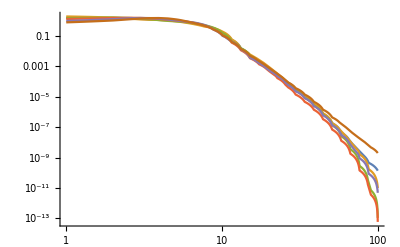

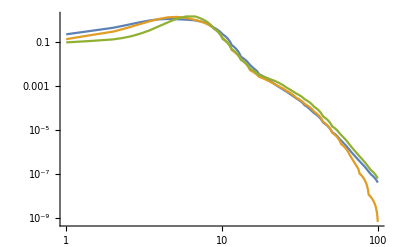

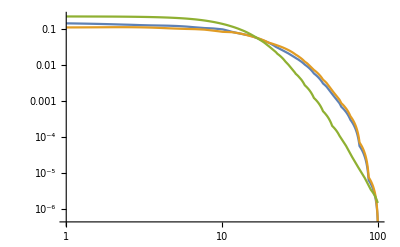

```mathematica
(*set path to form factor files*)
SetDirectory[NotebookDirectory[]<>"../../FormFactor_Coulomb_C1"];
(*set path to form factor files*)
(*For 5e, 4e, etc, could take 5e2 with occ=2 and 5e1 with occ=2; or 5e2 with occ=4. Here, I take occ=4 choice in the parameters section*)

L1a=Import["C4H10_1a1_grid_PW_largeQ.dat"];
L1e=Import["C4H10_1e2_grid_PW_largeQ.dat"];
L2a=Import["C4H10_2a1_grid_PW_largeQ.dat"];
L3a=Import["C4H10_3a1_grid_PW_largeQ.dat"];
L2e=Import["C4H10_2e2_grid_PW_largeQ.dat"];
L4a=Import["C4H10_4a1_grid_PW_largeQ.dat"];
L5a=Import["C4H10_5a1_grid_PW_largeQ.dat"];
L3e=Import["C4H10_3e2_grid_PW_largeQ.dat"];
L4e=Import["C4H10_4e2_grid_PW_largeQ.dat"];
L1a2=Import["C4H10_1a2_grid_PW_largeQ.dat"];
L5e=Import["C4H10_5e2_grid_PW_largeQ.dat"];
L6a=Import["C4H10_6a1_grid_PW_largeQ.dat"];
ResetDirectory[];

F1a=Interpolation[L1a,InterpolationOrder->1]
F1e=Interpolation[L1e,InterpolationOrder->1]
F2a=Interpolation[L2a,InterpolationOrder->1]
F3a=Interpolation[L3a,InterpolationOrder->1]
F2e=Interpolation[L2e,InterpolationOrder->1]
F4a=Interpolation[L4a,InterpolationOrder->1]
F5a=Interpolation[L5a,InterpolationOrder->1]
F3e=Interpolation[L3e,InterpolationOrder->1]
F4e=Interpolation[L4e,InterpolationOrder->1]
F1a2=Interpolation[L1a2,InterpolationOrder->1]
F5e=Interpolation[L5e,InterpolationOrder->1]
F6a=Interpolation[L6a,InterpolationOrder->1]

f1a=Function[{qx,Ex},If[qx>L1a[[-1]][[1]] ||Ex>L1a[[-1]][[2]],0,F1a[qx,Ex]]]
f1e=Function[{qx,Ex},If[qx>L1e[[-1]][[1]] ||Ex>L1e[[-1]][[2]],0,F1e[qx,Ex]]]
f2a=Function[{qx,Ex},If[qx>L2a[[-1]][[1]] ||Ex>L2a[[-1]][[2]],0,F2a[qx,Ex]]]
f3a=Function[{qx,Ex},If[qx>L3a[[-1]][[1]] ||Ex>L3a[[-1]][[2]],0,F3a[qx,Ex]]]
f2e=Function[{qx,Ex},If[qx>L2e[[-1]][[1]] ||Ex>L2e[[-1]][[2]],0,F2e[qx,Ex]]]
f4a=Function[{qx,Ex},If[qx>L4a[[-1]][[1]] ||Ex>L4a[[-1]][[2]],0,F4a[qx,Ex]]]
f5a=Function[{qx,Ex},If[qx>L5a[[-1]][[1]] ||Ex>L5a[[-1]][[2]],0,F5a[qx,Ex]]]
f3e=Function[{qx,Ex},If[qx>L3e[[-1]][[1]] ||Ex>L3e[[-1]][[2]],0,F3e[qx,Ex]]]
f4e=Function[{qx,Ex},If[qx>L4e[[-1]][[1]] ||Ex>L4e[[-1]][[2]],0,F4e[qx,Ex]]]
f1a2=Function[{qx,Ex},If[qx>L1a2[[-1]][[1]] ||Ex>L1a2[[-1]][[2]],0,F1a2[qx,Ex]]]
f5e=Function[{qx,Ex},If[qx>L5e[[-1]][[1]] ||Ex>L5e[[-1]][[2]],0,F5e[qx,Ex]]]
f6a=Function[{qx,Ex},If[qx>L6a[[-1]][[1]] ||Ex>L6a[[-1]][[2]],0,F6a[qx,Ex]]]

LogLogPlot[{f6a[qx,0.02],f5e[qx,0.02],f1a2[qx,0.02],f4e[qx,0.02],f3e[qx,0.02],f5a[qx,0.02]},{qx,1,100}]

LogLogPlot[{f4a[qx,0.02],f2e[qx,0.02],f3a[qx,0.02]},{qx,1,100}]

LogLogPlot[{f2a[qx,0.02],f1e[qx,0.02],f1a[qx,0.02]},{qx,1,100}]
```

## Parameters

```mathematica
Params6a=Association[
wnl->2,
Inl->11.13,
fionnl->f6a
];

Params5e=Association[
wnl->4,
Inl->11.75,
fionnl->f5e
];

Params1a2=Association[
wnl->2,
Inl->12.85,
fionnl->f1a2
];

Params4e=Association[
wnl->4,
Inl->13.71,
fionnl->f4e
];

Params3e=Association[
wnl->4,
Inl->15.03,
fionnl->f3e
];

Params5a=Association[
wnl->2,
Inl->15.91,
fionnl->f5a
];

Params4a=Association[
wnl->2,
Inl->18.58,
fionnl->f4a
];

Params2e=Association[
wnl->4,
Inl->21.83,
fionnl->f2e
];

Params3a=Association[
wnl->2,
Inl->24.83,
fionnl->f3a
];

Params2a=Association[
wnl->2,
Inl->304.94,
fionnl->f2a
];

Params1e=Association[
wnl->4,
Inl->304.94,
fionnl->f1e
];

Params1a=Association[
wnl->2,
Inl->305.43,
fionnl->f1a
];
```

## Rate calculation: FDM = 1

σe40 is the cross section relative to 10^-40 cm^2

#### dR/dE calculation: FDM = 1

```mathematica
TdRdE[mDMMeV0_,MNGeV0_,σe40_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

ρ=0.3;(*GeV cm^-3*)
σe=10^-40 σe40a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=794;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=  ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM=1

```mathematica
TdRETotal[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ6a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params6a],InterpolationOrder->1];
fσ5e=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params5e],InterpolationOrder->1];
fσ1a2=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1a2],InterpolationOrder->1];
fσ4e=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params4e],InterpolationOrder->1];
fσ3e=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params3e],InterpolationOrder->1];
fσ5a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params5a],InterpolationOrder->1];
fσ4a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params4a],InterpolationOrder->1];
fσ2e=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2e],InterpolationOrder->1];
fσ3a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params3a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2a],InterpolationOrder->1];
fσ1e=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1e],InterpolationOrder->1];
fσ1a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1a],InterpolationOrder->1];

Ftot[x_]:=fσ6a[x]+fσ5e[x]+fσ1a2[x]+fσ4e[x]+fσ3e[x]+fσ5a[x]+fσ4a[x]+fσ2e[x]+fσ3a[x]+fσ2a[x]+fσ1e[x]+fσ1a[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
AC4H10=58.2;
MNGeV=AC4H10 .931494; (*GeV*)
σ1=1; (*10^-40cm^2 cross section*)

TR30MeV=Quiet[TdRETotal[30,MNGeV,σ1]];
TR300MeV=Quiet[TdRETotal[300,MNGeV,σ1]];
TR1000MeV=Quiet[TdRETotal[1000,MNGeV,σ1]];

(*SetDirectory[NotebookDirectory[]];
Export["dRdE_C4H10_30MeV.dat",TR30MeV]
Export["dRdE_C4H10_300MeV.dat",TR300MeV]
Export["dRdE_C4H10_1000MeV.dat",TR1000MeV]
ResetDirectory[];*)
```

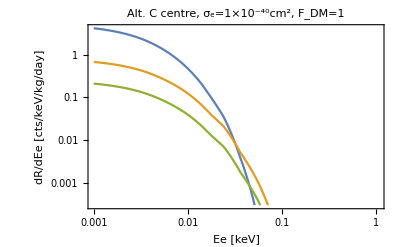

```mathematica
Show[ListLogLogPlot[{TR30MeV,TR300MeV,TR1000MeV},Joined->True,PlotRange->{{10^-3 ,1070 10^-3},{3 10^-4,Automatic}}],Frame->True,FrameLabel->{"Ee [keV]","dR/dEe [cts/keV/kg/day]"},PlotLabel->"Alt. C centre, σ_e="<>ToString[σ1]<>"×10^-40cm^2, F_DM=1"]
```

## Rate calculation: FDM = (alpha me / q)^2

σe37 is the cross section relative to 10^-37 cm^2

#### dR/dE calculation: FDM = (alpha me / q)^2

```mathematica
TdRdElightmed[mDMMeV0_,MNGeV0_,σe37_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

αEM=1/137.04;
ρ=0.3;(*GeV cm^-3*)
σe=10^-37 σe37a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
mekeV=1000. meMeV;(*keV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=794;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

FDM[qkeV_]:=(αEM mekeV/qkeV)^2;

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=   FDM[qkeV]^2ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM = (alpha me / q)^2

```mathematica
TdRETotallightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ6a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params6a],InterpolationOrder->1];
fσ5e=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params5e],InterpolationOrder->1];
fσ1a2=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1a2],InterpolationOrder->1];
fσ4e=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params4e],InterpolationOrder->1];
fσ3e=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params3e],InterpolationOrder->1];
fσ5a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params5a],InterpolationOrder->1];
fσ4a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params4a],InterpolationOrder->1];
fσ2e=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2e],InterpolationOrder->1];
fσ3a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params3a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2a],InterpolationOrder->1];
fσ1e=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1e],InterpolationOrder->1];
fσ1a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1a],InterpolationOrder->1];

Ftot[x_]:=fσ6a[x]+fσ5e[x]+fσ1a2[x]+fσ4e[x]+fσ3e[x]+fσ5a[x]+fσ4a[x]+fσ2e[x]+fσ3a[x]+fσ2a[x]+fσ1e[x]+fσ1a[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

### Calculate and Plot

```mathematica
AC4H10=58.2;
MNGeV=AC4H10 .931494; (*GeV*)
σ1=1; (*10^-37cm^2 cross section*)

TR30MeVlightmed=Quiet[TdRETotallightmed[30,MNGeV,σ1]];
TR300MeVlightmed=Quiet[TdRETotallightmed[300,MNGeV,σ1]];
TR1000MeVlightmed=Quiet[TdRETotallightmed[1000,MNGeV,σ1]];

(*SetDirectory[NotebookDirectory[]];
Export["dRdE_C4H10_30MeV_lightmed.dat",TR30MeVlightmed]
Export["dRdE_C4H10_300MeV_lightmed.dat",TR300MeVlightmed]
Export["dRdE_C4H10_1000MeV_lightmed.dat",TR1000MeVlightmed]
ResetDirectory[];*)
```

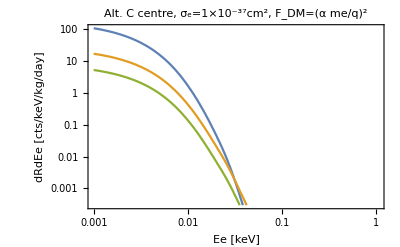

```mathematica
Show[ListLogLogPlot[{TR30MeVlightmed,TR300MeVlightmed,TR1000MeVlightmed},Joined->True,PlotRange->{{10^-3,1070 10^-3},{3 10^-4,Automatic}}],Frame->True,FrameLabel->{"Ee [keV]","dRdEe [cts/keV/kg/day]"},PlotLabel->"Alt. C centre, σ_e="<>ToString[σ1]<>"×10^-37cm^2, F_DM=(α me/q)^2"]
```